# Mathematica

It is the name of the software.
It works like Excel when we’re going to use a formulae, we have to be careful with what we use, the name, the list of parameters, etc.
There is a programming language involved, its name is Wolfram Language.
Mathematica offers plenty of tools, the most of them (we, here, now, are not interested in).
This presentation intention is to go as directly as possible to model and simulate

## Notebook

Or the way we must use in order to communicate with the kernel (of Wolfram).
We can create a document like this one.
We can interact with the kernel using Wolfram Language.
What we insert:

Title

Subtitle

Chapter

Section

Subsection

Subsubsection

Text

Code

Input

## Math operations

```mathematica
13+2
```

```mathematica
13-2
```

```mathematica
13*2
```

```mathematica
13/2
```

Numerical Value

```mathematica
N[23/3]
```

Square Brackets

```mathematica
N[23/3,2]
```

```mathematica
N[23/3,3]
```

```mathematica
N[23/3,4]
```

Free-Form input

23/3

```mathematica
Mod[23,2]
```

```mathematica
Quotient[23,2]
```

```mathematica
Round[23/3]
```

```mathematica
Round[23/3,2]
```

```mathematica
Round[23/3,3]
```

```mathematica
Round[23/3,4]
```

```mathematica
Round[23/3,5]
```

```mathematica
13/3
```

13/3

```mathematica
N[13/3]
```

4.33333

## Functions

```mathematica
Plus[2,3]
```

5

```mathematica
Subtract[5,2]
```

3

```mathematica
Times[2,3]
```

6

```mathematica
Times[2,Plus[3,4]]
```

14

```mathematica
Divide[7,2]
```

7/2

```mathematica
Power[3,2]
```

9

```mathematica
Max[2,7,3]
```

7

```mathematica
Max[{2,7,3}]
```

7

```mathematica
Min[2,7,3]
```

2

```mathematica
RandomInteger[10]
```

3

## Variables

```mathematica
rate = .18
```

```mathematica
3000 *rate
```

Case sensitive

```mathematica
Pi*14^2
```

```mathematica
pi*14^2
```

## Lists

alist = {2,3,4,5,19}

Curly Braces

```mathematica
Min[alist]
```

```mathematica
Max[alist]
```

```mathematica
Range[7]
```

```mathematica
Range[2,11]
```

```mathematica
Range[3,12,.5]
```

```mathematica
Goes to operator
```

```mathematica
Min[alist]
Max[alist]

Range[7]
Range[2,11]
Range[3,12,.5]

Goes to operator
```

## Symbolic expressions

```mathematica
Solve[a x^2+b x+c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

WolframAlphaQueryParseResults

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

WolframAlphaQueryParseResults

{1,4,9,16,25}

WolframAlphaQueryParseResults

CountryData (76.947 yr)

```mathematica
FunctionRange[CountryData Quantity[76.947,"Years"],{},x]
```

-76.947 CountryData+x (1 per year)==0

```mathematica
CountryData["Peru","LifeExpectancy"]
```

74.96 yr

WolframAlphaQueryResults

```mathematica
caffeine  molecule
```

Molecule[…]

toast + orange juice

WolframAlphaQueryResults

-Graphics-

## Last output cell

```mathematica
Table[i^2,{i,1,15}]
```

```mathematica
Total[%]
```

```mathematica
=Visualize the table of values for i^2, where i goes from 1 to 15.
```

## Create a function

```mathematica
doubleIt[x_]:=x*2
```

```mathematica
doubleIt[8]
```

```mathematica
powerOf[x_,exp_]:=x^exp
```

```mathematica
powerOf[3,2]
```

## Matrices

```mathematica
amat={{1,2,3,4},{9,8,7,6}}
```

{{1,2,3,4},{9,8,7,6}}

```mathematica
Dimensions[amat]
```

{2,4}

Det::matsq: Argument {{1,2,3,4},{9,8,7,6}} at position 1 is not a non-empty square matrix.

Det[{{1,2,3,4},{9,8,7,6}}]

```mathematica
bmat={{3,-1},{-2,3},{1,-2},{-1,3}}
```

{{3,-1},{-2,3},{1,-2},{-1,3}}

```mathematica
Dimensions[bmat]
```

{4,2}

```mathematica
cmat=amat.bmat
```

{{-2,11},{12,19}}

```mathematica
Dimensions[cmat]
```

```mathematica
{2,2}
```

{2,2}

```mathematica
Det[cmat]
```

-170

```mathematica
cmati=N[Inverse[cmat]]
```

{{-0.111765,0.0647059},{0.0705882,0.0117647}}

```mathematica
MatrixForm[cmat.cmati]
```

(1 | 0
0 | 1)

```mathematica
cmat+cmati
```

{{-2.11176,11.0647},{12.0706,19.0118}}

```mathematica
TypeOf[{1,21}]
```

TypeSpecifier[PackedArray[Integer64,LiteralType[1,Integer64]]]

## Referring to matrix rows and columns

```mathematica
mat1={{3,4,5,8},{-1,-3,-2,6},{9,-2,1,3}}
```

{{3,4,5,8},{-1,-3,-2,6},{9,-2,1,3}}

```mathematica
mat1[[2,2]]
```

-3

```mathematica
mat1[[2,2]]=-99
```

-99

```mathematica
mat1
```

{{3,4,5,8},{-1,-99,-2,6},{9,-2,1,3}}

## Plot a function

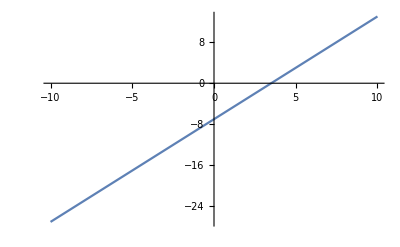

```mathematica
Plot[2x-7,{x,-10,10}]
```

WolframAlphaQueryParseResults

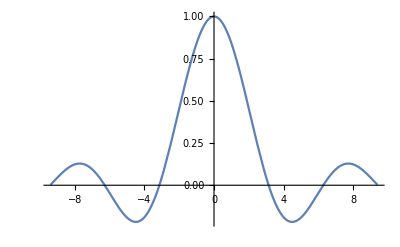

WolframAlphaQueryParseResults

-Graphics3D-

```mathematica
Manipulate[Plot[m* x-7,{x,-10,10}],{m,-10,10}]
```

```mathematica
Manipulate[Plot[Sin[freq*x],{x,0,2π}],{freq,1,5}]
```